### Instrumental Variables for Chains of Confounded Mediators, Nonlinear Case

We now consider the confounded mediator graph with an added instrument V prior to X.
w_i = (u^w)_i,
v_i = (u^v)_i,
x_i =gv_i+dw_i+(u^x)_i,
m_i = cx_i+ϵw_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

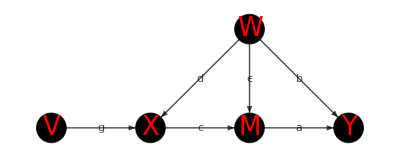

```mathematica
edges = {1->2,2->3,3->4,5->2,5->3,5->4};
vertices ={1,2,3,4,5};
vnames = {"V","X","M","Y","W"};
vweights={Subscript[σ, uV],Subscript[σ, uX],Subscript[σ, uM],Subscript[σ, uY],Subscript[σ, uW]};
vlabels = Thread[vertices->Map[Placed[#1,Center]&,vnames]];
eweights={g,c,a,d,ϵ,b};
elabels =Thread[edges->Map[Placed[Framed[Style[#1,18,Italic,Bold,Blue],Background->White,FrameStyle->White],"Middle"]&,eweights]];
vcoords = Thread[vertices->{{0,0},{1,0},{2,0},{3,0},{2,1}}];
vlookup=Thread[vnames->vertices];
vlookupname=Thread[vertices->vnames];
vweightsnou={Subscript[σ, V],Subscript[σ, X],Subscript[σ, M],Subscript[σ, Y],Subscript[σ, W]};
uvars=Map[Symbol["u"<>#]&,vnames];
vlookupweight=Flatten[{Thread[Map[Symbol["u"<>#]&,vnames]->vweights],Thread[Map[Symbol[#]&,vnames]->vweightsnou]}];
causalgraphiv2=Graph[edges,VertexLabels->vlabels,EdgeLabels->elabels,VertexWeight->vweights,EdgeWeight->eweights,GraphLayout->"LayeredEmbedding",VertexStyle->Black,VertexSize->0.3,VertexLabelStyle->Directive[Red,Italic,26],EdgeStyle->Black,VertexCoordinates->vcoords]
```

```mathematica
eweightlookup=Replace[Most@ArrayRules@WeightedAdjacencyMatrix[causalgraphiv2],{x_,y_}:>DirectedEdge[x,y],{2}]
uvarpairs=Permutations[uvars,{2}];
uprodrules=Flatten[{MapThread[#1*#1->#2^2&,{uvars,vweights}],Map[#[[1]]*#[[2]]->0&,uvarpairs]}]
```

{1->2→g,2->3→c,3->4→a,5->2→d,5->3→ϵ,5->4→b}

{uV^2→σ_uV^2,uX^2→σ_uX^2,uM^2→σ_uM^2,uY^2→σ_uY^2,uW^2→σ_uW^2,uV uX→0,uM uV→0,uV uY→0,uV uW→0,uV uX→0,uM uX→0,uX uY→0,uW uX→0,uM uV→0,uM uX→0,uM uY→0,uM uW→0,uV uY→0,uX uY→0,uM uY→0,uW uY→0,uV uW→0,uW uX→0,uM uW→0,uW uY→0}

Now we can apply this! Say we want to evaluate the expectation value E[ux*um | X,M]. First, we need to calculate the joint covariance between all four variables.

```mathematica
ParentNodes[graph_,node_]:=VertexInComponent[graph,Replace[node,vlookup],{1}];
ParentEdges[graph_,node_]:=Map[#->Replace[node,vlookup]&,ParentNodes[graph,node]];
NodeStructure[graph_,node_]:={Symbol[node]->Total[MapThread[Replace[#1,eweightlookup]*Symbol[Replace[#2,vlookupname]]&,{ParentEdges[graph,node],ParentNodes[graph,node]}]]+Symbol["u"<>node]};
NodesStructure[graph_,nodes_]:=Flatten[Table[NodeStructure[graph,node],{node,nodes}]];
GraphNodeStructure[graph_]:=Flatten[Table[NodeStructure[graph,node],{node,VertexList[graph]/.vlookupname}]];

NodeVariance[graph_,node_]:=ReplaceAll[{Symbol[node]^2->Total[MapThread[Replace[#1,eweightlookup]*Symbol[Replace[#2,vlookupname]]^2&,{ParentEdges[graph,node],ParentNodes[graph,node]}]]+Symbol["u"<>node]^2},vlookupweight];
GraphNodeVariance[graph_]:=Flatten[Table[NodeVariance[graph,node],{node,VertexList[graph]/.vlookupname}]];

uvarpairs=Permutations[uvars,{2}];
uprodrules=Flatten[{MapThread[#1*#1->#2^2&,{uvars,vweights}],Map[#[[1]]*#[[2]]->0&,uvarpairs]}]

NodeCovariance[graph_,node1_,node2_]:=ReplaceAll[Expand[ReplaceRepeated[Symbol[node1]*Symbol[node2],GraphNodeStructure[graph]]],uprodrules];

NodeCovarianceLinComb[graph_,nodes1_,coeffs1_,nodes2_,coeffs2_]:=
Total[Outer[Times,coeffs1,coeffs2]*Table[NodeCovariance[graph,node1,node2],{node1,nodes1},{node2,nodes2}],2];


NodesCovariance[graph_,nodes_]:=Table[NodeCovariance[graph,node1,node2],{node1,nodes},{node2,nodes}];
NodesCovarianceLinComb[graph_,lincombs_]:=Table[NodeCovarianceLinComb[graph,lincomb1[[1]],lincomb1[[2]],lincomb2[[1]],lincomb2[[2]]],{lincomb1,lincombs},{lincomb2,lincombs}];

RCRemove[a_?MatrixQ,row_?VectorQ,col_?VectorQ]:=Module[{nr,nc,krow,kcol},{nr,nc}=Dimensions[a];
krow=Complement[Range[1,nr],row];
kcol=Complement[Range[1,nc],col];
a[[krow,kcol]]];

CondMeans[graph_,varnodes_,condnodes_]:=Module[{Sig,SigA,SigB,SigAB,lA,lB},Sig=NodesCovariance[graph,Join[varnodes,condnodes]];
lA=Length[varnodes];
lB=Length[condnodes];
SigA=Sig[[1;;lA,1;;lA]];
SigB=Sig[[lA+1;;lA+lB,lA+1;;lA+lB]];
SigAB=Sig[[lA+1;;lA+lB,1;;lA]];
Transpose[SigAB].Inverse[SigB].Map[Symbol,condnodes]//Simplify
]

CondMeansLinComb[graph_,varlincombs_,condlincombs_]:=Module[{Sig,SigA,SigB,SigAB,lA,lB},Sig=NodesCovarianceLinComb[graph,Join[varlincombs,condlincombs]];
lA=Length[varlincombs];
lB=Length[condlincombs];
SigA=Sig[[1;;lA,1;;lA]];
SigB=Sig[[lA+1;;lA+lB,lA+1;;lA+lB]];
SigAB=Sig[[lA+1;;lA+lB,1;;lA]];
Transpose[SigAB].Inverse[SigB]//Simplify
]

CondVar[graph_,varnodes_,condnodes_]:=Module[{Sig,SigA,SigB,SigAB,lA,lB},Sig=NodesCovariance[graph,Join[varnodes,condnodes]];
lA=Length[varnodes];
lB=Length[condnodes];
SigA=Sig[[1;;lA,1;;lA]];
SigB=Sig[[lA+1;;lA+lB,lA+1;;lA+lB]];
SigAB=Sig[[lA+1;;lA+lB,1;;lA]];
SigA-Transpose[SigAB].Inverse[SigB].SigAB//Simplify
]
```

{uV^2→σ_uV^2,uX^2→σ_uX^2,uM^2→σ_uM^2,uY^2→σ_uY^2,uW^2→σ_uW^2,uV uX→0,uM uV→0,uV uY→0,uV uW→0,uV uX→0,uM uX→0,uX uY→0,uW uX→0,uM uV→0,uM uX→0,uM uY→0,uM uW→0,uV uY→0,uX uY→0,uM uY→0,uW uY→0,uV uW→0,uW uX→0,uM uW→0,uW uY→0}

```mathematica
NodeCovariance[graph_,node1_,node2_]:=ReplaceAll[Expand[ReplaceRepeated[Symbol[node1]*Symbol[node2],GraphNodeStructure[graph]]],uprodrules];
uV
uX
uW
uM
uW
```

uV

uX

uW

uM

uW

```mathematica
allstructure=GraphNodeStructure[causalgraphiv2]
allvariances=GraphNodeVariance[causalgraphiv2]
NodeCovariance[causalgraphiv2,"uX","X"]
Sig=NodesCovariance[causalgraphiv2,{"uX","uM","X","M"}];
MatrixForm[Sig]
CondMeans[causalgraphiv2,{"uX"},{"X","M"}]//MatrixForm
CondMeans[causalgraphiv2,{"uX","uM"},{"X","M"}]//MatrixForm
CondVar[causalgraphiv2,{"uX","uM"},{"X","M"}]//MatrixForm
```

{V→uV,X→uX+g V+d W,M→uM+c X+W ϵ,Y→a M+uY+b W,W→uW}

{σ_V^2→σ_uV^2,σ_X^2→σ_uX^2+g σ_V^2+d σ_W^2,σ_M^2→σ_uM^2+ϵ σ_W^2+c σ_X^2,σ_Y^2→a σ_M^2+σ_uY^2+b σ_W^2,σ_W^2→σ_uW^2}

σ_uX^2

(σ_uX^2 | 0 | σ_uX^2 | c σ_uX^2
0 | σ_uM^2 | 0 | σ_uM^2
σ_uX^2 | 0 | g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2 | c g^2 σ_uV^2+c d^2 σ_uW^2+d ϵ σ_uW^2+c σ_uX^2
c σ_uX^2 | σ_uM^2 | c g^2 σ_uV^2+c d^2 σ_uW^2+d ϵ σ_uW^2+c σ_uX^2 | σ_uM^2+c^2 g^2 σ_uV^2+c^2 d^2 σ_uW^2+2 c d ϵ σ_uW^2+ϵ^2 σ_uW^2+c^2 σ_uX^2)

(((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)))

(((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))
(σ_uM^2 (g^2 (M-c X) σ_uV^2+d (d M-c d X-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)))

(((g^2 ϵ^2 σ_uV^2 σ_uW^2+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2)) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)) | (d ϵ σ_uM^2 σ_uW^2 σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))
(d ϵ σ_uM^2 σ_uW^2 σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)) | (ϵ^2 σ_uM^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)))

```mathematica
CharacteristicPolynomial[Sig,x]//Factor
```

x^4-2 x^3 σ_uM^2-g^2 x^3 σ_uV^2-c^2 g^2 x^3 σ_uV^2+2 g^2 x^2 σ_uM^2 σ_uV^2+c^2 g^2 x^2 σ_uM^2 σ_uV^2-d^2 x^3 σ_uW^2-c^2 d^2 x^3 σ_uW^2-2 c d x^3 ϵ σ_uW^2-x^3 ϵ^2 σ_uW^2+2 d^2 x^2 σ_uM^2 σ_uW^2+c^2 d^2 x^2 σ_uM^2 σ_uW^2+2 c d x^2 ϵ σ_uM^2 σ_uW^2+x^2 ϵ^2 σ_uM^2 σ_uW^2+g^2 x^2 ϵ^2 σ_uV^2 σ_uW^2-g^2 x ϵ^2 σ_uM^2 σ_uV^2 σ_uW^2-2 x^3 σ_uX^2-c^2 x^3 σ_uX^2+4 x^2 σ_uM^2 σ_uX^2+c^2 x^2 σ_uM^2 σ_uX^2+g^2 x^2 σ_uV^2 σ_uX^2+c^2 g^2 x^2 σ_uV^2 σ_uX^2-2 g^2 x σ_uM^2 σ_uV^2 σ_uX^2-c^2 g^2 x σ_uM^2 σ_uV^2 σ_uX^2+d^2 x^2 σ_uW^2 σ_uX^2+c^2 d^2 x^2 σ_uW^2 σ_uX^2+2 c d x^2 ϵ σ_uW^2 σ_uX^2+2 x^2 ϵ^2 σ_uW^2 σ_uX^2-2 d^2 x σ_uM^2 σ_uW^2 σ_uX^2-c^2 d^2 x σ_uM^2 σ_uW^2 σ_uX^2-2 c d x ϵ σ_uM^2 σ_uW^2 σ_uX^2-2 x ϵ^2 σ_uM^2 σ_uW^2 σ_uX^2-g^2 x ϵ^2 σ_uV^2 σ_uW^2 σ_uX^2+g^2 ϵ^2 σ_uM^2 σ_uV^2 σ_uW^2 σ_uX^2

We will now seek to construct an estimator with improved bias or variance over the standard IV estimators on causal effects a and ca.

w_i = (u^w)_i,
v_i = (u^v)_i,
x_i =gv_i+dw_i+(u^x)_i,
m_i = cx_i+ϵw_i+(u^m)_i,
y_i = am_i+bw_i+(u^y)_i.

ResXV = X - gV = dW + uX
ResMX = M - cX = eW + uM

E_samples[ϵ/d]

Sample i = {(W),V,X,M,Y}


E[X - gV = dW + uX]
E[X] - g E[V] = d E[W] = 0

Unbiased
g
c
dW_i+uX_i
eW_i+uM_i

c+e/d (small bias)


c
eW_i+uM_i
W->X uniquely:   uW = (X-ux)/d

X = dW + uX
M = eW + cX + uM

e .dinv(dw) - e.dinv(dw + ux)
e(W) - e.dinv(dw + uX)
bias ~= E[dW.uX] + Ew[dW^2]




Key residual: Res’ = uM - e/d uX -  α*Cov(X,uM-e/d uX)*X/σ_X,    α ∈ [0,1]
such that Cov(X,Res’) = 0
but Cov(W,Cov(X,uM-e/d uX)*X/σ_X) != 0


V(Res) = σ_uM^2+ϵ^2/d^2 σ_uX^2 =~ 2
Cov(X,Res) =  -ϵ/d σ_uX^2 =~ -1
-- Need to check next order of these i.e. with V->X->M pathway

* Key result: Take res1 = M-((M.X)/(X.X))X as a vector-valued estimator
Then, Cov(X,res1) = E[M.X - M.X] = 0
but Cov(W,res1) = E[W.M - (M.X W.X)/(X.X)] = eE[W.W] - eE[(W.X W.X)/(X.X)] - E[(uM.X W.X)/(X.X)] != 0

This is counter to our intuition about uM - e/d uX, since:
Cov(uM - e/d uX, X) != 0
Cov(uM - e/d uX, W)  = 0

What about res2?

We have (biased) knowledge of OverHat[ϵ/d]
σ_uM^2= V(Res) + OverHat[ϵ/d]Cov(X,Res)
σ_uX^2= - Cov(X,Res)/(OverHat[ϵ/d])
--Can we re-insert samples from learned uM, uX variances to decrease bias?








Using E[A/B] = E[A]/E[B](1-cov[A,B]/(E[A]E[B})+V[B]/E[B]^2),
we have E[A/B] - E[A]/E[B] = (V[B]E[A])/E[B]^3-cov[A,B]/(E[B})^2

Empirically, we see E[(|E|)/(|D|)]=E[|E|]/E[|D|]=√[1/2+(e/d)^2] 
independent of a, b, c, absolute magnitude of e and d, noises,
but NOT g


ResMV-OverHat[edivd]*ResXV = um - e/d ux

```mathematica
OverHat[csimp]=(M.X)/(X.X)//Simplify
structureEqs={M->c*X+ϵ*W+uM,W->(X-uX-g*uV)/d};
cerror=OverHat[csimp]-c//.structureEqs//Simplify
noisenames={"uX","uM","uV"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv2,noisenames,{"X"}]
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
cerrorsimp=cerror/.condmeanreplace
cerrorsimp=cerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ,g}∈Reals}]&//Simplify
```

(M.X)/(X.X)

-c+((uM+c X-((g uV+uX-X) ϵ)/d).X)/(X.X)

{uX,uM,uV}

{(X σ_uX^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2),0,(g X σ_uV^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)}

{uX→(X σ_uX^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2),uM→0,uV→(g X σ_uV^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)}

-c+((c X-(ϵ (-X+(g^2 X σ_uV^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)+(X σ_uX^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)))/d).X)/(X.X)

(d ϵ σ_uW^2)/(g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)

```mathematica
{ĉ}=Estimator[{M},{X}];
ResMXSimp=M-ĉ X//Simplify;

{ĝ}=Estimator[{X},{V}];
ResXV=X-ĝ V//Simplify;

{OverHat[gc]}=Estimator[{M},{V}];
ResMV=M-OverHat[gc] V//Simplify;

OverHat[cIV]=OverHat[gc]/ĝ;
ResMX=M-OverHat[cIV] X//Simplify;
```

Set::shape: Lists {ĉ} and Estimator[{M},{X}] are not the same shape.

Set::shape: Lists {ĝ} and Estimator[{X},{V}] are not the same shape.

Set::shape: Lists {OverHat[gc]} and Estimator[{M},{V}] are not the same shape.

```mathematica
Clear[M,V,X,Y]
allstructure=GraphNodeStructure[causalgraphiv2]
OverHat[asimp]=(ResMXSimp.Y)/(ResMXSimp.M)//Simplify
OverHat[asimp]=(ResMXSimp.Y)/(ResMXSimp.M)//.{Y->a M+uY+b W,W->(X-uX-g*V)/d}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
OverHat[arem]=OverHat[arem]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
Numerator[OverHat[arem]]//ExpandAll
Denominator[OverHat[arem]]//ExpandAll
```

{V→uV,X→uX+g V+d W,M→uM+c X+W ϵ,Y→a M+uY+b W,W→uW}

((M-X ĉ).Y)/((M-X ĉ).M)

1/(d M.M-d (X ĉ).M)(a d M.M-b M.uX+d M.uY-b g M.V+b M.X-a d (X ĉ).M+b (X ĉ).uX-d (X ĉ).uY+b g (X ĉ).V-b (X ĉ).X)

OverHat[arem]

OverHat[arem]

1

```mathematica
OverHat[asimp]=(M.Y X.X-M.X X.Y)/(-M.X X.M+M.M X.X)//Simplify
structureEqs={Y->a*M+b*W+uY,W->(X-uX-g*uV)/d};
aerror=OverHat[asimp]-a//.structureEqs//Simplify
```

(M.Y X.X-M.X X.Y)/(-M.X X.M+M.M X.X)

-a+(-M.X X.(a M+uY-(b (g uV+uX-X))/d)+M.(a M+uY-(b (g uV+uX-X))/d) X.X)/(-M.X X.M+M.M X.X)

```mathematica
noisenames={"uX","uM","uY","uW","uV"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv2,noisenames,{"X","M"}]
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aerrorsimp=aerror/.condmeanreplace
aerrorsimp=aerror/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ,g}∈Reals}]&//Simplify
```

{uX,uM,uY,uW,uV}

{((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),(σ_uM^2 (g^2 (M-c X) σ_uV^2+d (d M-c d X-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),0,(σ_uW^2 (d X σ_uM^2+(M-c X) ϵ (g^2 σ_uV^2+σ_uX^2)))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),(g σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))}

{uX→((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uM→(σ_uM^2 (g^2 (M-c X) σ_uV^2+d (d M-c d X-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uY→0,uW→(σ_uW^2 (d X σ_uM^2+(M-c X) ϵ (g^2 σ_uV^2+σ_uX^2)))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uV→(g σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))}

-a+1/(-M.X X.M+M.M X.X)(M.(a M-1/d b (-X+(g^2 σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))+((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)))) X.X-M.X X.(a M-1/d b (-X+(g^2 σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))+((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)))))

(b ϵ σ_uW^2 (g^2 σ_uV^2+σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))

```mathematica
aerrorsimp/.{b->1,g->0,Subscript[σ, uW]^2->1,Subscript[σ, uV]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1,Subscript[σ, uY]^2->1}
```

ϵ/(1+d^2+ϵ^2)

```mathematica
OverHat[anum]=M.Y X.X-M.X X.Y//Simplify
structureEqs={Y->a*M+b*uW+uY,M->(c*X+ϵ*uW+uM),X->g*uV + d*uW + uX};
anumerror=OverHat[anum]//.structureEqs//Simplify
anumerror=TensorExpand[anumerror,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
anumerror=anumerror//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
```

M.Y X.X-M.X X.Y

-(g uV+d uW+uX).(b uW+uY+a (uM+c (g uV+d uW+uX)+uW ϵ)) (uM+c (g uV+d uW+uX)+uW ϵ).(g uV+d uW+uX)+(g uV+d uW+uX).(g uV+d uW+uX) (uM+c (g uV+d uW+uX)+uW ϵ).(b uW+uY+a (uM+c (g uV+d uW+uX)+uW ϵ))

ϵ (b+a ϵ) uW.uW (g^2 uV.uV+uX.uX)+a uM.uM (g^2 uV.uV+d^2 uW.uW+uX.uX)

ϵ (b+a ϵ) σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+a σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)

```mathematica
OverHat[adenom]=+M.M X.X-M.X X.M//Simplify
structureEqs={Y->a*M+b*uW+uY,M->(c*X+ϵ*uW+uM),X->g*uV + d*uW + uX};
adenomerror=OverHat[adenom]//.structureEqs//Simplify
adenomerror=TensorExpand[adenomerror,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
adenomerror=adenomerror//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
```

-M.X X.M+M.M X.X

-(g uV+d uW+uX).(uM+c (g uV+d uW+uX)+uW ϵ) (uM+c (g uV+d uW+uX)+uW ϵ).(g uV+d uW+uX)+(g uV+d uW+uX).(g uV+d uW+uX) (uM+c (g uV+d uW+uX)+uW ϵ).(uM+c (g uV+d uW+uX)+uW ϵ)

ϵ^2 uW.uW (g^2 uV.uV+uX.uX)+uM.uM (g^2 uV.uV+d^2 uW.uW+uX.uX)

ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)

```mathematica
anumerror/adenomerror - a //Simplify
```

(b ϵ σ_uW^2 (g^2 σ_uV^2+σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))

```mathematica
{OverHat[cplusedivd]}=Estimator[{M},{X}]
OverHat[edivd]=OverHat[cplusedivd] - OverHat[cIV]

ResNewMXsubed=ResMV-OverHat[edivd]*ResXV//Collect[#,{X,M,V}]&

regress M on V
ResNewMXold=ResMV-edivd[ResXV]//Collect[#,{X,M,V}]&
regress M on X
ResNewMX=ResMX-edivd[ResXV]//Collect[#,{X,M,V}]&

(e[W] + uM) - ϵ/d[dW + uX] = residual


RemNewMX = M - cX-edivd[X];
e[W] + uM = remainder
```

Set::shape: Lists {OverHat[cplusedivd]} and Estimator[{M},{X}] are not the same shape.

Estimator[{M},{X}]

OverHat[cplusedivd]-OverHat[gc]/(ĝ)

M+X (-OverHat[cplusedivd]+OverHat[gc]/(ĝ))+V (-OverHat[gc]+ĝ (OverHat[cplusedivd]-OverHat[gc]/(ĝ)))

M on regress V

M-edivd[X-V ĝ]-V OverHat[gc]

M on regress X

M-edivd[X-V ĝ]-(X OverHat[gc])/(ĝ)

Set::write: Tag Plus in -ϵ/d[dW+uX]+(uM+e[W]) is Protected.

residual

Set::write: Tag Plus in uM+e[W] is Protected.

remainder

```mathematica
Clear[M,V,X,Y]
allstructure=GraphNodeStructure[causalgraphiv2]
OverHat[arem]=(RemNewMX.Y)/(RemNewMX.M)
OverHat[arem]=(RemNewMX.Y)/(RemNewMX.M)//.{Y->a M+uY+b W,W->(X-uX-g*V)/d}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
OverHat[arem]=OverHat[arem]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
Numerator[OverHat[arem]]//ExpandAll
Denominator[OverHat[arem]]//ExpandAll
```

{V→uV,X→uX+g V+d W,M→uM+c X+W ϵ,Y→a M+uY+b W,W→uW}

((-cX+M-edivd[X]).Y)/((-cX+M-edivd[X]).M)

(a d cX.M-b cX.uX+d cX.uY-b g cX.V+b cX.X-a d M.M+b M.uX-d M.uY+b g M.V-b M.X+a d edivd[X].M-b edivd[X].uX+d edivd[X].uY-b g edivd[X].V+b edivd[X].X)/(d (cX.M-M.M+edivd[X].M))

(a d cX.M-b cX.uX+d cX.uY-b g cX.V+b cX.X-a d M.M+b M.uX-d M.uY+b g V.M-b X.M+a d edivd[X].M-b edivd[X].uX+d edivd[X].uY-b g edivd[X].V+b edivd[X].X)/(d (cX.M-M.M+edivd[X].M))

a d cX.M-b cX.uX+d cX.uY-b g cX.V+b cX.X-a d M.M+b M.uX-d M.uY+b g V.M-b X.M+a d edivd[X].M-b edivd[X].uX+d edivd[X].uY-b g edivd[X].V+b edivd[X].X

d cX.M-d M.M+d edivd[X].M

```mathematica
Clear[M,V,X,Y]
allstructure=GraphNodeStructure[causalgraphiv2]
OverHat[arem]=(RemNewMX.Y)/(RemNewMX.M)
Numarem=Numerator[OverHat[arem]]//TensorExpand[#,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
Denomarem=Denominator[OverHat[arem]]//TensorExpand[#,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
```

{V→uV,X→uX+g V+d W,M→uM+c X+W ϵ,Y→a M+uY+b W,W→uW}

((-cX+M-edivd[X]).Y)/((-cX+M-edivd[X]).M)

-cX.Y+M.Y-edivd[X].Y

-cX.M+M.M-edivd[X].M

```mathematica
OverHat[arem]=Numarem/Denomarem//Simplify
structureEqs={Y->a*M+b*W+uY,W->(X-uX-g*uV)/d};
aremerror=OverHat[arem]-a//.structureEqs//Simplify
noisenames={"uX","uM","uY","uW","uV"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv2,noisenames,{"X","M"}]
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aremerrorsimp=aremerror/.condmeanreplace
```

(cX.Y-M.Y+edivd[X].Y)/(cX.M-M.M+edivd[X].M)

-a+(cX.(a M+uY-(b (g uV+uX-X))/d)-M.(a M+uY-(b (g uV+uX-X))/d)+edivd[X].(a M+uY-(b (g uV+uX-X))/d))/(cX.M-M.M+edivd[X].M)

{uX,uM,uY,uW,uV}

{((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),(σ_uM^2 (g^2 (M-c X) σ_uV^2+d (d M-c d X-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),0,(σ_uW^2 (d X σ_uM^2+(M-c X) ϵ (g^2 σ_uV^2+σ_uX^2)))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),(g σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))}

{uX→((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uM→(σ_uM^2 (g^2 (M-c X) σ_uV^2+d (d M-c d X-X ϵ) σ_uW^2+(M-c X) σ_uX^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uY→0,uW→(σ_uW^2 (d X σ_uM^2+(M-c X) ϵ (g^2 σ_uV^2+σ_uX^2)))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)),uV→(g σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))}

-a+(cX.(a M-1/d b (-X+(g^2 σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))+((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))))-M.(a M-1/d b (-X+(g^2 σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))+((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))))+edivd[X].(a M-1/d b (-X+(g^2 σ_uV^2 (X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2))/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2))+((X σ_uM^2+ϵ (-d M+c d X+X ϵ) σ_uW^2) σ_uX^2)/(ϵ^2 σ_uW^2 (g^2 σ_uV^2+σ_uX^2)+σ_uM^2 (g^2 σ_uV^2+d^2 σ_uW^2+σ_uX^2)))))/(cX.M-M.M+edivd[X].M)

```mathematica
b Subscript[σ, uW]^2 (-ϵ (-d M.M+(c d+ϵ) X.M) (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2)+d M.X (d Subscript[σ, uM]^2-c ϵ (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2))+(c d+ϵ) X.X (-d Subscript[σ, uM]^2+c ϵ (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2)))/((d M.M-(c d+ϵ) X.M) (ϵ^2 Subscript[σ, uW]^2 (g^2 Subscript[σ, uV]^2+Subscript[σ, uX]^2)+Subscript[σ, uM]^2 (g^2 Subscript[σ, uV]^2+d^2 Subscript[σ, uW]^2+Subscript[σ, uX]^2)))/.{X.M->M.X,g->0}//Simplify
```

(b σ_uW^2 (d ϵ M.M σ_uX^2+(c d+ϵ) X.X (-d σ_uM^2+c ϵ σ_uX^2)+M.X (d^2 σ_uM^2-ϵ (2 c d+ϵ) σ_uX^2)))/((d M.M-(c d+ϵ) M.X) (ϵ^2 σ_uW^2 σ_uX^2+σ_uM^2 (d^2 σ_uW^2+σ_uX^2)))

```mathematica
OverHat[remVar]=RemNewMX.RemNewMX//.{Y->a M+uY+b W,W->(X-uX-g*uV)/d}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
OverHat[remVar]=OverHat[remVar]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
OverHat[remVar]=OverHat[remVar]//.{M->c*X+uM+e*uW,X->g*uV+d*uW+uX}//Simplify
OverHat[remVar]=TensorExpand[OverHat[remVar],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]//.{uM.uV->0,uM.uX->0,uM.uW->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
OverHat[remVar]=OverHat[remVar]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
```

cX.cX-cX.M+cX.edivd[X]-M.cX+M.M-M.edivd[X]+edivd[X].cX-edivd[X].M+edivd[X].edivd[X]

cX.cX-cX.M+cX.edivd[X]-M.cX+M.M-M.edivd[X]+edivd[X].cX-edivd[X].M+edivd[X].edivd[X]

cX.cX-cX.(uM+e uW+c (g uV+d uW+uX))+cX.edivd[g uV+d uW+uX]-(uM+e uW+c (g uV+d uW+uX)).cX+(uM+e uW+c (g uV+d uW+uX)).(uM+e uW+c (g uV+d uW+uX))-(uM+e uW+c (g uV+d uW+uX)).edivd[g uV+d uW+uX]+edivd[g uV+d uW+uX].cX-edivd[g uV+d uW+uX].(uM+e uW+c (g uV+d uW+uX))+edivd[g uV+d uW+uX].edivd[g uV+d uW+uX]

cX.cX-cX.uM-c g cX.uV-c d cX.uW-e cX.uW-c cX.uX+cX.edivd[g uV+d uW+uX]-uM.cX+uM.uM-uM.edivd[g uV+d uW+uX]-c g uV.cX+c^2 g^2 uV.uV-c g uV.edivd[g uV+d uW+uX]-c d uW.cX-e uW.cX+c^2 d^2 uW.uW+2 c d e uW.uW+e^2 uW.uW-c d uW.edivd[g uV+d uW+uX]-e uW.edivd[g uV+d uW+uX]-c uX.cX+c^2 uX.uX-c uX.edivd[g uV+d uW+uX]+edivd[g uV+d uW+uX].cX-edivd[g uV+d uW+uX].uM-c g edivd[g uV+d uW+uX].uV-c d edivd[g uV+d uW+uX].uW-e edivd[g uV+d uW+uX].uW-c edivd[g uV+d uW+uX].uX+edivd[g uV+d uW+uX].edivd[g uV+d uW+uX]

cX.cX-cX.uM-c g cX.uV-c d cX.uW-e cX.uW-c cX.uX+cX.edivd[g uV+d uW+uX]-uM.cX-uM.edivd[g uV+d uW+uX]-c g uV.cX-c g uV.edivd[g uV+d uW+uX]-c d uW.cX-e uW.cX-c d uW.edivd[g uV+d uW+uX]-e uW.edivd[g uV+d uW+uX]-c uX.cX-c uX.edivd[g uV+d uW+uX]+edivd[g uV+d uW+uX].cX-edivd[g uV+d uW+uX].uM-c g edivd[g uV+d uW+uX].uV-c d edivd[g uV+d uW+uX].uW-e edivd[g uV+d uW+uX].uW-c edivd[g uV+d uW+uX].uX+edivd[g uV+d uW+uX].edivd[g uV+d uW+uX]+σ_uM^2+c^2 g^2 σ_uV^2+c^2 d^2 σ_uW^2+2 c d e σ_uW^2+e^2 σ_uW^2+c^2 σ_uX^2

```mathematica
OverHat[aremDen]=RemNewMX.M//.{Y->a M+uY+b W,W->(X-uX-g*uV)/d}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,ϵ,g}∈Reals}]&//Simplify
OverHat[aremDen]=OverHat[aremDen]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
OverHat[aremDen]=OverHat[aremDen]//.{M->c*X+uM+ϵ*uW,X->g*uV+d*uW+uX}//Simplify
OverHat[aremDen]=TensorExpand[OverHat[aremDen],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,ϵ,g}∈Reals}]//.{uM.uV->0,uM.uX->0,uM.uW->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
OverHat[aremDen]=OverHat[aremDen]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
```

-cX.M+M.M-edivd[X].M

-cX.M+M.M-edivd[X].M

-cX.(uM+c (g uV+d uW+uX)+uW ϵ)+(uM+c (g uV+d uW+uX)+uW ϵ).(uM+c (g uV+d uW+uX)+uW ϵ)-edivd[g uV+d uW+uX].(uM+c (g uV+d uW+uX)+uW ϵ)

-cX.uM-c g cX.uV-c d cX.uW-ϵ cX.uW-c cX.uX+uM.uM+c^2 g^2 uV.uV+c^2 d^2 uW.uW+2 c d ϵ uW.uW+ϵ^2 uW.uW+c^2 uX.uX-edivd[g uV+d uW+uX].uM-c g edivd[g uV+d uW+uX].uV-c d edivd[g uV+d uW+uX].uW-ϵ edivd[g uV+d uW+uX].uW-c edivd[g uV+d uW+uX].uX

-cX.uM-c g cX.uV-c d cX.uW-ϵ cX.uW-c cX.uX-edivd[g uV+d uW+uX].uM-c g edivd[g uV+d uW+uX].uV-c d edivd[g uV+d uW+uX].uW-ϵ edivd[g uV+d uW+uX].uW-c edivd[g uV+d uW+uX].uX+σ_uM^2+c^2 g^2 σ_uV^2+c^2 d^2 σ_uW^2+2 c d ϵ σ_uW^2+ϵ^2 σ_uW^2+c^2 σ_uX^2

```mathematica
OverHat[aremNum]=RemNewMX.Y//.{Y->a M+uY+b W,W->(X-uX-g*uV)/d}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,ϵ,g}∈Reals}]&//Simplify
OverHat[aremNum]=OverHat[aremNum]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
OverHat[aremNum]=OverHat[aremNum]//.{M->c*X+uM+ϵ*uW,X->g*uV+d*uW+uX}//Simplify
OverHat[aremNum]=TensorExpand[OverHat[aremNum],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
OverHat[aremNum]=OverHat[aremNum]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
```

-1/d(a d cX.M-b g cX.uV-b cX.uX+d cX.uY+b cX.X-a d M.M+b g M.uV+b M.uX-d M.uY-b M.X+a d edivd[X].M-b g edivd[X].uV-b edivd[X].uX+d edivd[X].uY+b edivd[X].X)

-1/d(a d cX.M-b g cX.uV-b cX.uX+d cX.uY+b cX.X-a d M.M+b g M.uV+b M.uX-d M.uY-b X.M+a d edivd[X].M-b g edivd[X].uV-b edivd[X].uX+d edivd[X].uY+b edivd[X].X)

1/d(b g cX.uV+b cX.uX-b cX.(g uV+d uW+uX)-d cX.uY-a d cX.(uM+c (g uV+d uW+uX)+uW ϵ)+b (g uV+d uW+uX).(uM+c (g uV+d uW+uX)+uW ϵ)-b g (uM+c (g uV+d uW+uX)+uW ϵ).uV-b (uM+c (g uV+d uW+uX)+uW ϵ).uX+d (uM+c (g uV+d uW+uX)+uW ϵ).uY+a d (uM+c (g uV+d uW+uX)+uW ϵ).(uM+c (g uV+d uW+uX)+uW ϵ)+b g edivd[g uV+d uW+uX].uV+b edivd[g uV+d uW+uX].uX-b edivd[g uV+d uW+uX].(g uV+d uW+uX)-d edivd[g uV+d uW+uX].uY-a d edivd[g uV+d uW+uX].(uM+c (g uV+d uW+uX)+uW ϵ))

-a cX.uM-a c g cX.uV-b cX.uW-a c d cX.uW-a ϵ cX.uW-a c cX.uX-cX.uY+a uM.uM+a c^2 g^2 uV.uV+b c d uW.uW+a c^2 d^2 uW.uW+b ϵ uW.uW+2 a c d ϵ uW.uW+a ϵ^2 uW.uW+a c^2 uX.uX-a edivd[g uV+d uW+uX].uM-a c g edivd[g uV+d uW+uX].uV-b edivd[g uV+d uW+uX].uW-a c d edivd[g uV+d uW+uX].uW-a ϵ edivd[g uV+d uW+uX].uW-a c edivd[g uV+d uW+uX].uX-edivd[g uV+d uW+uX].uY

-a cX.uM-a c g cX.uV-b cX.uW-a c d cX.uW-a ϵ cX.uW-a c cX.uX-cX.uY-a edivd[g uV+d uW+uX].uM-a c g edivd[g uV+d uW+uX].uV-b edivd[g uV+d uW+uX].uW-a c d edivd[g uV+d uW+uX].uW-a ϵ edivd[g uV+d uW+uX].uW-a c edivd[g uV+d uW+uX].uX-edivd[g uV+d uW+uX].uY+a σ_uM^2+a c^2 g^2 σ_uV^2+b c d σ_uW^2+a c^2 d^2 σ_uW^2+b ϵ σ_uW^2+2 a c d ϵ σ_uW^2+a ϵ^2 σ_uW^2+a c^2 σ_uX^2

```mathematica
Clear[M,V,X,Y]
allstructure=GraphNodeStructure[causalgraphiv2]
OverHat[ares]=(ResNewMX.Y)/(ResNewMX.M)
Numares=Numerator[OverHat[ares]](V.X)(V.V)//TensorExpand[#,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
Denomares=Denominator[OverHat[ares]](V.X)(V.V)//TensorExpand[#,Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,g}∈Reals}]&//Simplify
```

{V→uV,X→uX+g V+d W,M→uM+c X+W ϵ,Y→a M+uY+b W,W→uW}

((M-edivd[X-V ĝ]-(X OverHat[gc])/(ĝ)).Y)/((M-edivd[X-V ĝ]-(X OverHat[gc])/(ĝ)).M)

-(V.V V.X ((X OverHat[gc]).Y+(-M.Y+edivd[X-V ĝ].Y) ĝ))/(ĝ)

-(V.V V.X ((X OverHat[gc]).M+(-M.M+edivd[X-V ĝ].M) ĝ))/(ĝ)

```mathematica
OverHat[ares]=Numares/Denomares//Simplify
structureEqs={Y->a*M+b*W+uY,W->(X-uX-g*uV)/d};
areserror=OverHat[ares]-a//.structureEqs//Simplify
```

((X OverHat[gc]).Y+(-M.Y+edivd[X-V ĝ].Y) ĝ)/((X OverHat[gc]).M+(-M.M+edivd[X-V ĝ].M) ĝ)

-a+((X OverHat[gc]).(a M+uY-(b (g uV+uX-X))/d)+(-M.(a M+uY-(b (g uV+uX-X))/d)+edivd[X-V ĝ].(a M+uY-(b (g uV+uX-X))/d)) ĝ)/((X OverHat[gc]).M+(-M.M+edivd[X-V ĝ].M) ĝ)

```mathematica
OverHat[aresDen]=ResNewMXold.M//.{Y->a M+uY+b W,W->(X-uX-g*uV)/d,V->uV}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]&//Simplify;
OverHat[aresDen]=OverHat[aresDen]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify;
OverHat[aresDen]=OverHat[aresDen]//.{M->c*X+uM+ϵ*uW,X->g*uV+d*uW+uX}//Simplify;
OverHat[aresDen]=TensorExpand[OverHat[aresDen],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify;
OverHat[aresDen]=OverHat[aresDen]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
OverHat[aresDen]=TensorExpand[OverHat[aresDen],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
OverHat[aresDen]=OverHat[aresDen]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
OverHat[aresDen]=Collect[OverHat[aresDen],a]
```

-edivd[g uV+d uW+uX-uV ĝ].uM-c g edivd[g uV+d uW+uX-uV ĝ].uV-c d edivd[g uV+d uW+uX-uV ĝ].uW-ϵ edivd[g uV+d uW+uX-uV ĝ].uW-c edivd[g uV+d uW+uX-uV ĝ].uX-(uV OverHat[gc]).uM-c g (uV OverHat[gc]).uV-c d (uV OverHat[gc]).uW-ϵ (uV OverHat[gc]).uW-c (uV OverHat[gc]).uX+σ_uM^2+c^2 g^2 σ_uV^2+c^2 d^2 σ_uW^2+2 c d ϵ σ_uW^2+ϵ^2 σ_uW^2+c^2 σ_uX^2

-edivd[g uV+d uW+uX-uV ĝ].uM-c g edivd[g uV+d uW+uX-uV ĝ].uV-c d edivd[g uV+d uW+uX-uV ĝ].uW-ϵ edivd[g uV+d uW+uX-uV ĝ].uW-c edivd[g uV+d uW+uX-uV ĝ].uX-(uV OverHat[gc]).uM-c g (uV OverHat[gc]).uV-c d (uV OverHat[gc]).uW-ϵ (uV OverHat[gc]).uW-c (uV OverHat[gc]).uX+σ_uM^2+c^2 g^2 σ_uV^2+c^2 d^2 σ_uW^2+2 c d ϵ σ_uW^2+ϵ^2 σ_uW^2+c^2 σ_uX^2

-edivd[g uV+d uW+uX-uV ĝ].uM-c g edivd[g uV+d uW+uX-uV ĝ].uV-c d edivd[g uV+d uW+uX-uV ĝ].uW-ϵ edivd[g uV+d uW+uX-uV ĝ].uW-c edivd[g uV+d uW+uX-uV ĝ].uX-(uV OverHat[gc]).uM-c g (uV OverHat[gc]).uV-c d (uV OverHat[gc]).uW-ϵ (uV OverHat[gc]).uW-c (uV OverHat[gc]).uX+σ_uM^2+c^2 g^2 σ_uV^2+c^2 d^2 σ_uW^2+2 c d ϵ σ_uW^2+ϵ^2 σ_uW^2+c^2 σ_uX^2

«1 more identical outputs»

```mathematica
noise=1
aresDenSolve=OverHat[aresDen]/.{c->1,Subscript[σ, uW]^2->noise,Subscript[σ, uX]^2->noise,Subscript[σ, uM]^2->noise}
aresDenSol=Solve[aresDenSolve==0,e]
Plot[e/.aresDenSol[[1]],{d,-10,10}]
```

1

2+d^2+2 d ϵ+ϵ^2-edivd[g uV+d uW+uX-uV ĝ].uM-g edivd[g uV+d uW+uX-uV ĝ].uV-d edivd[g uV+d uW+uX-uV ĝ].uW-ϵ edivd[g uV+d uW+uX-uV ĝ].uW-edivd[g uV+d uW+uX-uV ĝ].uX-(uV OverHat[gc]).uM-g (uV OverHat[gc]).uV-d (uV OverHat[gc]).uW-ϵ (uV OverHat[gc]).uW-(uV OverHat[gc]).uX+g^2 σ_uV^2

{}

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-Graphics-

```mathematica
OverHat[aresNum]=ResNewMXold.Y//.{Y->a M+uY+b W,W->(X-uX-g*uV)/d,V->uV}//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]&//Simplify;
OverHat[aresNum]=OverHat[aresNum]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify;
OverHat[aresNum]=OverHat[aresNum]//.{M->c*X+uM+ϵ*uW,X->g*uV+d*uW+uX}//Simplify;
OverHat[aresNum]=TensorExpand[OverHat[aresNum],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify;
OverHat[aresNum]=OverHat[aresNum]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
OverHat[aresNum]=TensorExpand[OverHat[aresNum],Assumptions->
{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals,vweights ∈Reals,{a,b,c,d,e,ϵ,g}∈Reals}]//.{uY.uM->0,uY.uX->0,uY.uV->0,uY.uW->0,uM.uY->0,uM.uV->0,uM.uX->0,uM.uW->0,uX.uY->0,uX.uM->0,uX.uV->0,uX.uW->0,uV.uY->0,uV.uM->0,uV.uX->0,uV.uW->0,uW.uY->0,uW.uM->0,uW.uV->0,uW.uX->0}//Simplify
OverHat[aresNum]=OverHat[aresNum]//.{uV.uV->Subscript[σ, uV]^2,uW.uW->Subscript[σ, uW]^2,uX.uX->Subscript[σ, uX]^2,uM.uM->Subscript[σ, uM]^2}//Simplify
OverHat[aresNum]=Collect[OverHat[aresNum],a]
```

-a edivd[g uV+d uW+uX-uV ĝ].uM-a c g edivd[g uV+d uW+uX-uV ĝ].uV-b edivd[g uV+d uW+uX-uV ĝ].uW-a c d edivd[g uV+d uW+uX-uV ĝ].uW-a ϵ edivd[g uV+d uW+uX-uV ĝ].uW-a c edivd[g uV+d uW+uX-uV ĝ].uX-edivd[g uV+d uW+uX-uV ĝ].uY-a (uV OverHat[gc]).uM-a c g (uV OverHat[gc]).uV-b (uV OverHat[gc]).uW-a c d (uV OverHat[gc]).uW-a ϵ (uV OverHat[gc]).uW-a c (uV OverHat[gc]).uX-(uV OverHat[gc]).uY+a σ_uM^2+a c^2 g^2 σ_uV^2+b c d σ_uW^2+a c^2 d^2 σ_uW^2+b ϵ σ_uW^2+2 a c d ϵ σ_uW^2+a ϵ^2 σ_uW^2+a c^2 σ_uX^2

-a edivd[g uV+d uW+uX-uV ĝ].uM-a c g edivd[g uV+d uW+uX-uV ĝ].uV-b edivd[g uV+d uW+uX-uV ĝ].uW-a c d edivd[g uV+d uW+uX-uV ĝ].uW-a ϵ edivd[g uV+d uW+uX-uV ĝ].uW-a c edivd[g uV+d uW+uX-uV ĝ].uX-edivd[g uV+d uW+uX-uV ĝ].uY-a (uV OverHat[gc]).uM-a c g (uV OverHat[gc]).uV-b (uV OverHat[gc]).uW-a c d (uV OverHat[gc]).uW-a ϵ (uV OverHat[gc]).uW-a c (uV OverHat[gc]).uX-(uV OverHat[gc]).uY+a σ_uM^2+a c^2 g^2 σ_uV^2+b c d σ_uW^2+a c^2 d^2 σ_uW^2+b ϵ σ_uW^2+2 a c d ϵ σ_uW^2+a ϵ^2 σ_uW^2+a c^2 σ_uX^2

-a edivd[g uV+d uW+uX-uV ĝ].uM-a c g edivd[g uV+d uW+uX-uV ĝ].uV-b edivd[g uV+d uW+uX-uV ĝ].uW-a c d edivd[g uV+d uW+uX-uV ĝ].uW-a ϵ edivd[g uV+d uW+uX-uV ĝ].uW-a c edivd[g uV+d uW+uX-uV ĝ].uX-edivd[g uV+d uW+uX-uV ĝ].uY-a (uV OverHat[gc]).uM-a c g (uV OverHat[gc]).uV-b (uV OverHat[gc]).uW-a c d (uV OverHat[gc]).uW-a ϵ (uV OverHat[gc]).uW-a c (uV OverHat[gc]).uX-(uV OverHat[gc]).uY+a σ_uM^2+a c^2 g^2 σ_uV^2+b c d σ_uW^2+a c^2 d^2 σ_uW^2+b ϵ σ_uW^2+2 a c d ϵ σ_uW^2+a ϵ^2 σ_uW^2+a c^2 σ_uX^2

-b edivd[g uV+d uW+uX-uV ĝ].uW-edivd[g uV+d uW+uX-uV ĝ].uY-b (uV OverHat[gc]).uW-(uV OverHat[gc]).uY+b c d σ_uW^2+b ϵ σ_uW^2+a (-edivd[g uV+d uW+uX-uV ĝ].uM-c g edivd[g uV+d uW+uX-uV ĝ].uV-c d edivd[g uV+d uW+uX-uV ĝ].uW-ϵ edivd[g uV+d uW+uX-uV ĝ].uW-c edivd[g uV+d uW+uX-uV ĝ].uX-(uV OverHat[gc]).uM-c g (uV OverHat[gc]).uV-c d (uV OverHat[gc]).uW-ϵ (uV OverHat[gc]).uW-c (uV OverHat[gc]).uX+σ_uM^2+c^2 g^2 σ_uV^2+c^2 d^2 σ_uW^2+2 c d ϵ σ_uW^2+ϵ^2 σ_uW^2+c^2 σ_uX^2)

```mathematica
DynamicModule[{a},Column[{Dynamic@Plot[aresBiasNum,{e,0,5},PlotRange->{All,{-3,3}}],Slider[Dynamic@d,{0,5},Label]}]]
```

```mathematica
aresBias=OverHat[(aresNum]/OverHat[aresDen])-a//Simplify
aresBiasNum[d_,e_]=aresBias/.{b->1,c->1,Subscript[σ, uW]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1}//Simplify
aresBiasNum[d,e]
aresBiasNum[0.5,1.499]
Manipulate[Plot[aresBiasNum[d,e],{e,0,5},PlotRange->{All,{-3,3}}],{d,0,5,Labeled[Panel@Column[{Slider[##,ImageSize->250],Graphics[{},Axes->{True,False},Ticks->{Subdivide[##&@@#2,5],None},ImageSize->250,PlotRange->{#2,{0,.05}}]},Alignment->Center,Spacings->0],#,Right]&}]
Solve[2 d-e+d^2 (d+e)==0,e]
```

```mathematica
OverHat[slopeMuM]=(ResNewMX.M)/(ResNewMX.ResNewMX)//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals}]&//Simplify
OverHat[slopeMuM]=OverHat[slopeMuM]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
Numerator[OverHat[slopeMuM]]//ExpandAll
Denominator[OverHat[slopeMuM]]//ExpandAll
```

(ĝ (-(X OverHat[gc]).M+(M.M-edivd[X-V ĝ].M) ĝ))/((X OverHat[gc]).(X OverHat[gc])+ĝ (-M.(X OverHat[gc])+edivd[X-V ĝ].(X OverHat[gc])-(X OverHat[gc]).M+(X OverHat[gc]).edivd[X-V ĝ]+M.M ĝ-M.edivd[X-V ĝ] ĝ-edivd[X-V ĝ].M ĝ+edivd[X-V ĝ].edivd[X-V ĝ] ĝ))

(ĝ (-(X OverHat[gc]).M+(M.M-edivd[X-V ĝ].M) ĝ))/((X OverHat[gc]).(X OverHat[gc])+ĝ (-M.(X OverHat[gc])+edivd[X-V ĝ].(X OverHat[gc])-(X OverHat[gc]).M+(X OverHat[gc]).edivd[X-V ĝ]+M.M ĝ-M.edivd[X-V ĝ] ĝ-edivd[X-V ĝ].M ĝ+edivd[X-V ĝ].edivd[X-V ĝ] ĝ))

-(X OverHat[gc]).M ĝ+M.M (ĝ)^2-edivd[X-V ĝ].M (ĝ)^2

(X OverHat[gc]).(X OverHat[gc])-M.(X OverHat[gc]) ĝ+edivd[X-V ĝ].(X OverHat[gc]) ĝ-(X OverHat[gc]).M ĝ+(X OverHat[gc]).edivd[X-V ĝ] ĝ+M.M (ĝ)^2-M.edivd[X-V ĝ] (ĝ)^2-edivd[X-V ĝ].M (ĝ)^2+edivd[X-V ĝ].edivd[X-V ĝ] (ĝ)^2

```mathematica
OverHat[slopeYuM]=(ResNewMX.Y)/(ResNewMX.ResNewMX)//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals}]&//Simplify
OverHat[slopeYuM]=OverHat[slopeYuM]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
Numerator[OverHat[slopeYuM]]//ExpandAll
Denominator[OverHat[slopeYuM]]//ExpandAll
```

(ĝ (-(X OverHat[gc]).Y+(M.Y-edivd[X-V ĝ].Y) ĝ))/((X OverHat[gc]).(X OverHat[gc])+ĝ (-M.(X OverHat[gc])+edivd[X-V ĝ].(X OverHat[gc])-(X OverHat[gc]).M+(X OverHat[gc]).edivd[X-V ĝ]+M.M ĝ-M.edivd[X-V ĝ] ĝ-edivd[X-V ĝ].M ĝ+edivd[X-V ĝ].edivd[X-V ĝ] ĝ))

(ĝ (-(X OverHat[gc]).Y+(M.Y-edivd[X-V ĝ].Y) ĝ))/((X OverHat[gc]).(X OverHat[gc])+ĝ (-M.(X OverHat[gc])+edivd[X-V ĝ].(X OverHat[gc])-(X OverHat[gc]).M+(X OverHat[gc]).edivd[X-V ĝ]+M.M ĝ-M.edivd[X-V ĝ] ĝ-edivd[X-V ĝ].M ĝ+edivd[X-V ĝ].edivd[X-V ĝ] ĝ))

-(X OverHat[gc]).Y ĝ+M.Y (ĝ)^2-edivd[X-V ĝ].Y (ĝ)^2

(X OverHat[gc]).(X OverHat[gc])-M.(X OverHat[gc]) ĝ+edivd[X-V ĝ].(X OverHat[gc]) ĝ-(X OverHat[gc]).M ĝ+(X OverHat[gc]).edivd[X-V ĝ] ĝ+M.M (ĝ)^2-M.edivd[X-V ĝ] (ĝ)^2-edivd[X-V ĝ].M (ĝ)^2+edivd[X-V ĝ].edivd[X-V ĝ] (ĝ)^2

```mathematica
OverHat[numslopeYuM]=Numerator[OverHat[slopeYuM]]//Collect[#,{V.X}]&
OverHat[numslopeMuM]=Numerator[OverHat[slopeMuM]]//Collect[#,{V.X}]&
OverHat[aNewIV]=Collect[Simplify[OverHat[numslopeYuM]/-(V.X)],{V.X}]/Collect[Simplify[OverHat[numslopeMuM]/-(V.X)],{V.X}]
```

ĝ (-(X OverHat[gc]).Y+(M.Y-edivd[X-V ĝ].Y) ĝ)

ĝ (-(X OverHat[gc]).M+(M.M-edivd[X-V ĝ].M) ĝ)

((X OverHat[gc]).Y+(-M.Y+edivd[X-V ĝ].Y) ĝ)/((X OverHat[gc]).M+(-M.M+edivd[X-V ĝ].M) ĝ)

The above estimator for a can be written in the more manifestly-symmetric form, where it is clear that the denominator is simply the numerator /. {Y→M}:
((V.X)^2 X.M X.X V.Y+V.X ( V.V (X.X)^2 M.Y-2 (X.X)^2 V.M V.Y-V.V X.X X.M X.Y)+V.M V.V (X.X)^2 X.Y)/((V.X)^2 X.M X.X V.M+V.X (V.V (X.X)^2 M.M-2  (X.X)^2(V.M)^2-V.V X.X(X.M)^2)+V.M V.V(X.X)^2 X.M)

Another approach is possible, where instead of retrieving ϵ/dfrom the difference between the IV estimator on C and the backdoor estimator on C+ϵ/d, we extract ϵ/d from the following ratio of residuals:
OverHat[(ϵ/d)]=(m-(m.v)/(x.v)x)/(x-(x.v)/(v.v)v)
We have been a bit notationally irresponsible here, as we are dividing two vectors which are not exactly parallel, due to the noise terms u^m and u^x. On the average they should be parallel, so we take the estimator to be the ratio of magnitudes:
OverHat[(ϵ/d)]=(|m-(m.v)/(x.v)x|)/(|x-(x.v)/(v.v)v|)
More specifically,

```mathematica
OverHat[edivd2]=(ResMX.ResMX)/(ResXV.ResXV)//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals}]&//Simplify
OverHat[edivd2]=OverHat[edivd2]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify
```

((X OverHat[gc]).(X OverHat[gc])+ĝ (-M.(X OverHat[gc])-(X OverHat[gc]).M+M.M ĝ))/((X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ)) (ĝ)^2)

((X OverHat[gc]).(X OverHat[gc])+ĝ (-M.(X OverHat[gc])-(X OverHat[gc]).M+M.M ĝ))/((X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ)) (ĝ)^2)

```mathematica
ResNewMX2=ResMV-OverHat[edivd2]*ResXV//Simplify//Collect[#,{X,M,V}]&
```

M+X (-((X OverHat[gc]).(X OverHat[gc]))/((X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ)) (ĝ)^2)-(-M.(X OverHat[gc])-(X OverHat[gc]).M+M.M ĝ)/((X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ)) ĝ))+V (((X OverHat[gc]).(X OverHat[gc]))/((X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ)) ĝ)+(-M.(X OverHat[gc])-(X OverHat[gc]).M+M.M ĝ)/(X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ))-OverHat[gc])

```mathematica
OverHat[slopeMuM2]=(ResNewMX2.M)/(ResNewMX2.ResNewMX2)//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals}]&//Simplify;
OverHat[slopeMuM2]=OverHat[slopeMuM2]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify;
Numerator[OverHat[slopeMuM2]]//ExpandAll;
Denominator[OverHat[slopeMuM2]]//ExpandAll;
```

```mathematica
OverHat[slopeYuM2]=(ResNewMX2.Y)/(ResNewMX2.ResNewMX2)//TensorExpand[#,Assumptions->{{V.V,V.X,V.M,X.V,X.X,X.M,M.V,M.X,M.M}∈Reals}]&//Simplify;
OverHat[slopeYuM2]=OverHat[slopeYuM2]//.{X.V->V.X,M.V->V.M,M.X->X.M}//Simplify;
Numerator[OverHat[slopeYuM2]]//ExpandAll;
Denominator[OverHat[slopeYuM2]]//ExpandAll;
```

```mathematica
OverHat[numslopeYuM2]=Numerator[OverHat[slopeYuM2]]//Collect[#,{V.X}]&
OverHat[numslopeMuM2]=Numerator[OverHat[slopeMuM2]]//Collect[#,{V.X}]&
OverHat[aNewIV2]=Collect[Simplify[OverHat[numslopeYuM2]/(V.X)^2],{V.X}]/Collect[Simplify[OverHat[numslopeMuM2]/(V.X)^2],{V.X}]
```

M.Y+(-(X ((X OverHat[gc]).(X OverHat[gc])+ĝ (-M.(X OverHat[gc])-(X OverHat[gc]).M+M.M ĝ)))/((X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ)) (ĝ)^2)).Y+(V (((X OverHat[gc]).(X OverHat[gc]))/((X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ)) ĝ)-(M.(X OverHat[gc])+(X OverHat[gc]).M-M.M ĝ)/(X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ))-OverHat[gc])).Y

M.M+(-(X ((X OverHat[gc]).(X OverHat[gc])+ĝ (-M.(X OverHat[gc])-(X OverHat[gc]).M+M.M ĝ)))/((X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ)) (ĝ)^2)).M+(V (((X OverHat[gc]).(X OverHat[gc]))/((X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ)) ĝ)-(M.(X OverHat[gc])+(X OverHat[gc]).M-M.M ĝ)/(X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ))-OverHat[gc])).M

(M.Y+(-(X ((X OverHat[gc]).(X OverHat[gc])+ĝ (-M.(X OverHat[gc])-(X OverHat[gc]).M+M.M ĝ)))/((X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ)) (ĝ)^2)).Y+(V (((X OverHat[gc]).(X OverHat[gc]))/((X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ)) ĝ)-(M.(X OverHat[gc])+(X OverHat[gc]).M-M.M ĝ)/(X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ))-OverHat[gc])).Y)/(M.M+(-(X ((X OverHat[gc]).(X OverHat[gc])+ĝ (-M.(X OverHat[gc])-(X OverHat[gc]).M+M.M ĝ)))/((X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ)) (ĝ)^2)).M+(V (((X OverHat[gc]).(X OverHat[gc]))/((X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ)) ĝ)-(M.(X OverHat[gc])+(X OverHat[gc]).M-M.M ĝ)/(X.X-X.(V ĝ)-(V ĝ).X+(V ĝ).(V ĝ))-OverHat[gc])).M)

The above estimator for a can be written in the more manifestly-symmetric form, where it is clear that the denominator is simply the numerator /. {Y→M}:
((V.X)^2 X.M X.X V.Y+V.X ( V.V (X.X)^2 M.Y-2 (X.X)^2 V.M V.Y-V.V X.X X.M X.Y)+V.M V.V (X.X)^2 X.Y)/((V.X)^2 X.M X.X V.M+V.X (V.V (X.X)^2 M.M-2  (X.X)^2(V.M)^2-V.V X.X(X.M)^2)+V.M V.V(X.X)^2 X.M)

```mathematica
structureEqs={Y->a*M+b*W+uY,W->(M-uM)/d};
aerror=OverHat[aIV]-a//.structureEqs;
```

```mathematica
noisenames={"uX","uM","uY"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv,noisenames,{"X","M"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aerrorsimp=aerror/.condmeanreplace
//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify
```

{uX,uM,uY}

Table::iterb: Iterator {node,VertexList[causalgraphiv]} does not have appropriate bounds.

ReplaceRepeated::reps: {Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Table::iterb: Iterator {node,VertexList[causalgraphiv]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ReplaceRepeated::reps: {Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

{uX→((-X (M^2//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])+M (M X//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])) (uX X//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])+(M uX//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]) (X (M X//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])-M (X^2//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])))/((M X//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])^2-(M^2//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]) (X^2//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])),uM→((-X (M^2//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])+M (M X//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])) (uM X//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])+(M uM//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]) (X (M X//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])-M (X^2//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])))/((M X//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])^2-(M^2//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]) (X^2//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])),uY→((-X (M^2//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])+M (M X//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])) (uY X//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])+(M uY//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]) (X (M X//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])-M (X^2//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])))/((M X//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])^2-(M^2//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]) (X^2//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]))}

-a+OverHat[aIV]

```mathematica
aIVcorr=(OverHat[ca]-c*a)(ĉ-c)//Expand//.structureEqs;
noisenames={"uX","uM","uY","M","Y"};
noises=Map[Symbol,noisenames]

condmeans=CondMeans[causalgraphiv,noisenames,{"X"}];
condmeanreplace=MapThread[#1->#2&,{noises,condmeans}]
aIVcorrsimp=aIVcorr/.condmeanreplace//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d, ϵ}∈Reals}]&//Simplify
```

{uX,uM,uY,M,Y}

Table::iterb: Iterator {node,VertexList[causalgraphiv]} does not have appropriate bounds.

ReplaceRepeated::reps: {Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Table::iterb: Iterator {node,VertexList[causalgraphiv]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ReplaceRepeated::reps: {Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

{uX→(X (uX X//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]))/(X^2//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]),uM→(X (uM X//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]))/(X^2//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]),uY→(X (uY X//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]))/(X^2//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]),M→(X (M X//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]))/(X^2//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]),Y→(X (X Y//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}]))/(X^2//.Table[NodeStructure[causalgraphiv,node],{node,VertexList[causalgraphiv]}])}

(c-ĉ) (a c-OverHat[ca])

```mathematica
aerrorsimp/.{b->1,d->1,ϵ->0.5,Subscript[σ, uW]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1}
aerrorsimp/.{b->1,d->1,ϵ->0.1,Subscript[σ, uW]^2->1,Subscript[σ, uX]^2->1,Subscript[σ, uM]^2->1}
```

-a+OverHat[aIV]

-a+OverHat[aIV]

### Power Series for Nonlinear Assessment, IFDC Estimator

```mathematica
orderd=3;
ordere=2;
maxorder=Max[orderd,ordere];
Clear[d,e,dseries,eseries,dinv,cd,ce];
dfunc[x_]:=Sum[d[i]*x^i,{i,orderd}];
efunc[x_]:=Sum[e[i]*x^i,{i,ordere}];

dseries=Series[dfunc[x],{x,0,maxorder}];
eseries=Series[efunc[x],{x,0,maxorder}];
dinv=InverseSeries[dseries];
edivd=ComposeSeries[eseries,dinv];
```

```mathematica
xrule={x->ux+dfunc[uW]};
resifdc=X^2 M;
edivdX=edivd;
edivdXuX=edivd/.{x->x-ux};
rem=um+edivdXuX-edivdX//Simplify//Collect[#,x]&//Collect[#,ux]&
GetVariables[expr_]:=Select[DeleteDuplicates@Level[expr,Depth@expr],Head[#]==Symbol&]
EvenMoment[n_]=(n-1)Abs[n-3];
EvenMoment[0]=1;
NoiseMoments[expr_,vars_]:=If[AllTrue[Exponent[expr,vars],EvenQ],Total[Flatten[CoefficientList[expr,vars]]]*Times @@(EvenMoment[Exponent[expr,#]] Subscript[σ,ToString[#]]^Exponent[expr,#]&/@vars),0]
NoiseMoments[um^2,{um,ux,uw}];
Exponent[um^2,{um,ux,uw}];
remw=rem//.xrule//Simplify//Expand[#,uw]&
m=um+c*x+efunc[uw]//.xrule//Expand[#,uw]&;
remdenom=remw*m//Expand[#]&;
remdenomlist=NoiseMoments[#,{um,ux,uw}]&/@List@@remdenom;
remdenomsum=Total[remdenomlist]//Simplify;
```

SeriesData::sdatv: First argument -ux+x is not a valid variable.

um+(-(e[1] x)/d[1]+((d[2] e[1]-d[1] e[2]) x^2)/d[1]^3+((-2 d[2]^2 e[1]+d[1] d[3] e[1]+2 d[1] d[2] e[2]) x^3)/d[1]^5+O[x]^4)+((e[1] (-ux+x))/d[1]+((-d[2] e[1]+d[1] e[2]) (-ux+x)^2)/d[1]^3+((2 d[2]^2 e[1]-d[1] d[3] e[1]-2 d[1] d[2] e[2]) (-ux+x)^3)/d[1]^5+O[-ux+x]^4)

SeriesData::sdatv: First argument ux+uW d[1]+uW^2 d[2]+uW^3 d[3] is not a valid variable.

SeriesData::sdatv: First argument uW d[1]+uW^2 d[2]+uW^3 d[3] is not a valid variable.

um+((e[1] uW (d[1]+uW (d[2]+uW d[3])))/d[1]+((-d[2] e[1]+d[1] e[2]) (uW (d[1]+uW (d[2]+uW d[3])))^2)/d[1]^3+1/d[1]^5(2 d[2]^2 e[1]-d[1] d[3] e[1]-2 d[1] d[2] e[2]) (uW (d[1]+uW (d[2]+uW d[3])))^3+O[uW (d[1]+uW (d[2]+uW d[3]))]^4)+(-(e[1] (ux+uW (d[1]+uW (d[2]+uW d[3]))))/d[1]+((d[2] e[1]-d[1] e[2]) (ux+uW (d[1]+uW (d[2]+uW d[3])))^2)/d[1]^3+1/d[1]^5(-2 d[2]^2 e[1]+d[1] d[3] e[1]+2 d[1] d[2] e[2]) (ux+uW (d[1]+uW (d[2]+uW d[3])))^3+O[ux+uW (d[1]+uW (d[2]+uW d[3]))]^4)

```mathematica
y=uy+a*m+b*uw//.xrule//Expand[#,uw]&;
remnum=remw*y//Expand[#]&;
remnumlist=NoiseMoments[#,{um,ux,uw}]&/@List@@remnum;
remnumsum=Total[remnumlist]//Simplify
```

a σ_um^2+((e[1] uW (d[1]+uW (d[2]+uW d[3])))/d[1]+((-d[2] e[1]+d[1] e[2]) (uW (d[1]+uW (d[2]+uW d[3])))^2)/d[1]^3+1/d[1]^5(2 d[2]^2 e[1]-d[1] d[3] e[1]-2 d[1] d[2] e[2]) (uW (d[1]+uW (d[2]+uW d[3])))^3+O[uW (d[1]+uW (d[2]+uW d[3]))]^4) (uy+a c uW (d[1]+uW (d[2]+uW d[3]))+a e[2] σ_uw^2)+(-(e[1] (ux+uW (d[1]+uW (d[2]+uW d[3]))))/d[1]+((d[2] e[1]-d[1] e[2]) (ux+uW (d[1]+uW (d[2]+uW d[3])))^2)/d[1]^3+1/d[1]^5(-2 d[2]^2 e[1]+d[1] d[3] e[1]+2 d[1] d[2] e[2]) (ux+uW (d[1]+uW (d[2]+uW d[3])))^3+O[ux+uW (d[1]+uW (d[2]+uW d[3]))]^4) (uy+a c uW (d[1]+uW (d[2]+uW d[3]))+a e[2] σ_uw^2)

```mathematica
rembiasratio=remnumsum/remdenomsum-a//Simplify
rembiasratio/.{Subscript[σ, "ux"]^2->0}
```

(uy (((e[1] uW (d[1]+uW (d[2]+uW d[3])))/d[1]+((-d[2] e[1]+d[1] e[2]) (uW (d[1]+uW (d[2]+uW d[3])))^2)/d[1]^3+1/d[1]^5(2 d[2]^2 e[1]-d[1] d[3] e[1]-2 d[1] d[2] e[2]) (uW (d[1]+uW (d[2]+uW d[3])))^3+O[uW (d[1]+uW (d[2]+uW d[3]))]^4)+(-(e[1] (ux+uW (d[1]+uW (d[2]+uW d[3]))))/d[1]+((d[2] e[1]-d[1] e[2]) (ux+uW (d[1]+uW (d[2]+uW d[3])))^2)/d[1]^3+1/d[1]^5(-2 d[2]^2 e[1]+d[1] d[3] e[1]+2 d[1] d[2] e[2]) (ux+uW (d[1]+uW (d[2]+uW d[3])))^3+O[ux+uW (d[1]+uW (d[2]+uW d[3]))]^4)))/(σ_um^2+((e[1] uW (d[1]+uW (d[2]+uW d[3])))/d[1]+((-d[2] e[1]+d[1] e[2]) (uW (d[1]+uW (d[2]+uW d[3])))^2)/d[1]^3+1/d[1]^5(2 d[2]^2 e[1]-d[1] d[3] e[1]-2 d[1] d[2] e[2]) (uW (d[1]+uW (d[2]+uW d[3])))^3+O[uW (d[1]+uW (d[2]+uW d[3]))]^4) (c uW (d[1]+uW (d[2]+uW d[3]))+e[2] σ_uw^2)+(-(e[1] (ux+uW (d[1]+uW (d[2]+uW d[3]))))/d[1]+((d[2] e[1]-d[1] e[2]) (ux+uW (d[1]+uW (d[2]+uW d[3])))^2)/d[1]^3+1/d[1]^5(-2 d[2]^2 e[1]+d[1] d[3] e[1]+2 d[1] d[2] e[2]) (ux+uW (d[1]+uW (d[2]+uW d[3])))^3+O[ux+uW (d[1]+uW (d[2]+uW d[3]))]^4) (c uW (d[1]+uW (d[2]+uW d[3]))+e[2] σ_uw^2))

(uy (((e[1] uW (d[1]+uW (d[2]+uW d[3])))/d[1]+((-d[2] e[1]+d[1] e[2]) (uW (d[1]+uW (d[2]+uW d[3])))^2)/d[1]^3+1/d[1]^5(2 d[2]^2 e[1]-d[1] d[3] e[1]-2 d[1] d[2] e[2]) (uW (d[1]+uW (d[2]+uW d[3])))^3+O[uW (d[1]+uW (d[2]+uW d[3]))]^4)+(-(e[1] (ux+uW (d[1]+uW (d[2]+uW d[3]))))/d[1]+((d[2] e[1]-d[1] e[2]) (ux+uW (d[1]+uW (d[2]+uW d[3])))^2)/d[1]^3+1/d[1]^5(-2 d[2]^2 e[1]+d[1] d[3] e[1]+2 d[1] d[2] e[2]) (ux+uW (d[1]+uW (d[2]+uW d[3])))^3+O[ux+uW (d[1]+uW (d[2]+uW d[3]))]^4)))/(σ_um^2+((e[1] uW (d[1]+uW (d[2]+uW d[3])))/d[1]+((-d[2] e[1]+d[1] e[2]) (uW (d[1]+uW (d[2]+uW d[3])))^2)/d[1]^3+1/d[1]^5(2 d[2]^2 e[1]-d[1] d[3] e[1]-2 d[1] d[2] e[2]) (uW (d[1]+uW (d[2]+uW d[3])))^3+O[uW (d[1]+uW (d[2]+uW d[3]))]^4) (c uW (d[1]+uW (d[2]+uW d[3]))+e[2] σ_uw^2)+(-(e[1] (ux+uW (d[1]+uW (d[2]+uW d[3]))))/d[1]+((d[2] e[1]-d[1] e[2]) (ux+uW (d[1]+uW (d[2]+uW d[3])))^2)/d[1]^3+1/d[1]^5(-2 d[2]^2 e[1]+d[1] d[3] e[1]+2 d[1] d[2] e[2]) (ux+uW (d[1]+uW (d[2]+uW d[3])))^3+O[ux+uW (d[1]+uW (d[2]+uW d[3]))]^4) (c uW (d[1]+uW (d[2]+uW d[3]))+e[2] σ_uw^2))

```mathematica
(*from https://mathematica.stackexchange.com/a/34780*)
ClearAll[moment]
moment[{0...}]=1;
moment[x_List]/;Total[x]==2:=If[Length[#]==1,σ[#[[1]],#[[1]]],σ[#[[1]],#[[2]]]]&@Position[x,y_?Positive][[All,1]];
moment[x_List]:=moment[x]=Module[{i=LengthWhile[x,#==0&]+1,x2=x},x2[[i]]--;
Sum[If[x2[[j]]>0,x2[[j]] σ[i,j] moment@MapAt[#-1&,x2,j],0],{j,i,Length[x]}]];
moment[{8}]
```

105 σ[1,1]^4

### Power Series for Nonlinear Assessment, Remainder Estimator

```mathematica
Clear[a,b,c,d,um,ux,uw,m,x,w]
orderd=3;
ordere=1;
maxorder=Max[orderd,ordere];
bigorder=3
Clear[d,e,dseries,eseries,dinv,cd,ce];
dfunc[X_]:=Sum[d[i]*X^i,{i,orderd}];
efunc[X_]:=Sum[e[i]*X^i,{i,ordere}];
dfunc2[X_]:=Sum[d[i]*X^i,{i,2}];

dseries=Series[dfunc[X],{X,0,bigorder}]
dseries2=Series[dfunc2[X],{X,0,bigorder}]
eseries=Series[efunc[X],{X,0,bigorder}]
dinv=InverseSeries[dseries];
dinv2=InverseSeries[dseries2]
edivd=ComposeSeries[eseries,dinv]//Collect[#,X]&;
edivd2=ComposeSeries[eseries,dinv2]//Collect[#,X]&;
```

3

d[1] X+d[2] X^2+d[3] X^3+O[X]^4

d[1] X+d[2] X^2+O[X]^4

e[1] X+O[X]^4

X/d[1]-(d[2] X^2)/d[1]^3+(2 d[2]^2 X^3)/d[1]^5+O[X]^4

```mathematica
edivdX=Normal[edivd]//.{X->x};
edivdXuX=Normal[edivd]//.{X->x-ux};
rem=um+edivdXuX-edivdX//Simplify//Collect[#,x]&//Collect[#,ux]&;
GetVariables[expr_]:=Select[DeleteDuplicates@Level[expr,Depth@expr],Head[#]==Symbol&]
EvenMoment[n_]=(n-1)Abs[n-3];
EvenMoment[0]=1;
NoiseMoments[expr_,vars_]:=If[AllTrue[Exponent[expr,vars],EvenQ],Total[Flatten[CoefficientList[expr,vars]]]*Times @@(EvenMoment[Exponent[expr,#]] Subscript[σ,ToString[#]]^Exponent[expr,#]&/@vars),0]
NoiseMoments[um^2,{um,ux,uw}];
Exponent[um^2,{um,ux,uw}];
xrule={x->ux+dfunc[uw]};
remw=rem//.xrule//Simplify//Expand[#,uw]&;
m=um+c*x+efunc[uw]//.xrule//Expand[#,uw]&;
remdenom=remw*m//Expand[#]&;
remdenomlist=NoiseMoments[#,{um,ux,uw}]&/@List@@remdenom;
remdenomsum=Total[remdenomlist]//Simplify;
```

```mathematica
remdenomsumcheck=remdenomsum/.{d[3]->0}
```

σ_um^2+1/d[1]^5 e[1] σ_ux^2 (3 d[1] (-3 c d[1] d[2]^2-2 d[2]^2 e[1]) σ_uw^2-36 c d[2]^4 σ_uw^4-c (d[1]^4+6 d[2]^2 σ_ux^2))

```mathematica
y=uy+a*m+b*uw//.xrule//Expand[#]&;
remnum=remw*y//Expand[#]&;
remnumlist=NoiseMoments[#,{um,ux,uw,uy}]&/@List@@remnum;
remnumsum=Total[remnumlist]//Simplify;
remnumsum/.{Subscript[σ, "ux"]^2->0}
```

a σ_um^2

```mathematica
rembiasratio=remnumsum/remdenomsum-a//Simplify//Expand;
rembiasratio/.{d[3]->0,d[1]->d}//Simplify;
rembiasratio/.{e[3]->0,e[1]->e, d[1]->Subscript[d, 1],d[2]->Subscript[d, 2],d[3]->Subscript[d, 3]}//Simplify
rembiasratio/.{Subscript[σ, "uw"]->1,Subscript[σ, "ux"]->1,Subscript[σ, "um"]->1,d[1]->1,e[1]->2,b->1,c->1,d[1]->Subscript[d, 1],d[2]->Subscript[d, 2],d[3]->Subscript[d, 3]}//Simplify
rembiasratio/.{Subscript[σ, "ux"]->0}
```

(3 b e σ_uw^2 (d_1^2 d_3-6 d_2^2 d_3 σ_uw^2+d_1 (-2 d_2^2+3 d_3^2 σ_uw^2)) σ_ux^2)/(d_1^5 σ_um^2-c e d_1^4 σ_ux^2+6 c e d_1^3 d_3 σ_uw^2 σ_ux^2+3 e d_1^2 σ_uw^2 (-3 c d_2^2+d_3 (e+12 c d_3 σ_uw^2)) σ_ux^2-6 e d_2^2 σ_ux^2 (6 c d_2^2 σ_uw^4+3 e d_3 σ_uw^4+30 c d_3^2 σ_uw^6+c σ_ux^2)+3 e d_1 σ_ux^2 (-2 d_2^2 σ_uw^2 (e+9 c d_3 σ_uw^2)+d_3 (3 e d_3 σ_uw^4+30 c d_3^2 σ_uw^6+c σ_ux^2)))

(6 (2 d_2^2-d_3) (1+3 d_3))/(1+72 d_2^4-30 d_3-108 d_3^2-180 d_3^3+18 d_2^2 (3+10 d_3+20 d_3^2))

0

```mathematica
rembiasratiosimple=rembiasratio/.{Subscript[σ, "ux"]->0.2,Subscript[σ, "uw"]->0.2,Subscript[σ, "um"]->0.2,b->1,c->1,d[1]->1,e[1]->2}//Simplify
```

(d[2]^2 (4.16667+0.5 d[3])+(-2.08333-0.25 d[3]) d[3])/(8.68056+1. d[2]^4-10.4167 d[3]-1.5 d[3]^2-0.1 d[3]^3+d[2]^2 (18.75+2.5 d[3]+0.2 d[3]^2))

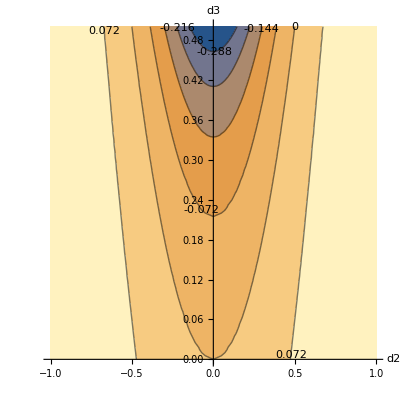

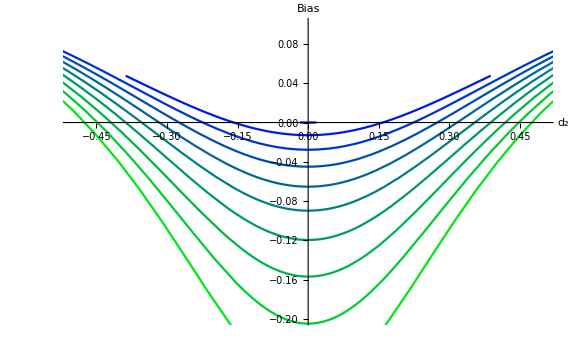

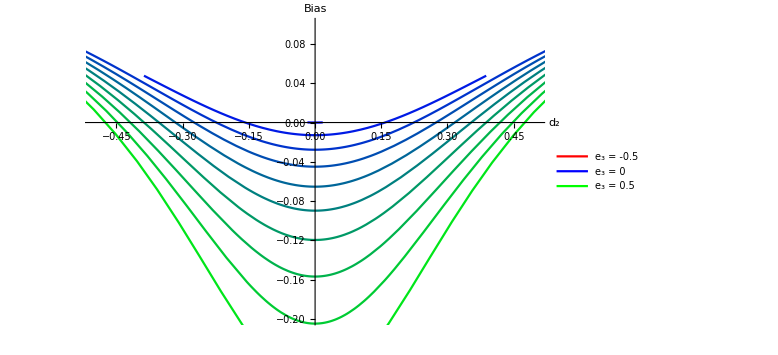

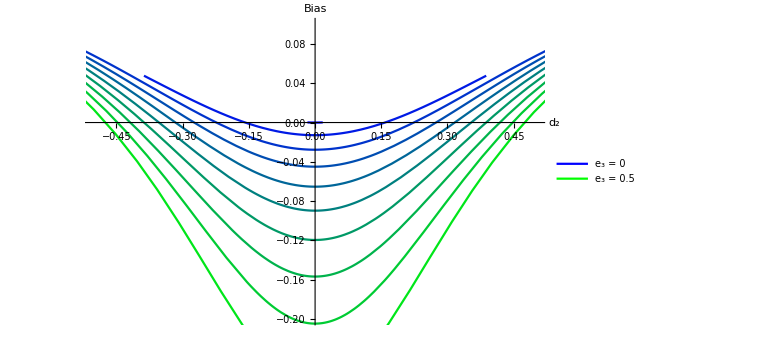

```mathematica
Clear[makeplotd,makeplote,makeplotde]
SetOptions[ContourPlot,BaseStyle->FontSize->18];
rembiasplote[e2_,e3_]:=rembiasratiosimple/.{e[2]->e2,e[3]->e3}
makeplote[]:=ContourPlot[rembiasplote[e2,e3],{e2,-1,1},{e3,-1,1},ContourLabels->True,Frame->False,Axes->True,AxesLabel->Automatic];
makelineplote[]:=Show[Table[Plot[rembiasplote[Subscript[e, 2],e3],{Subscript[e, 2],-1,1},PlotStyle->RGBColor[-e3/0.5,e3/0.5,(1-Abs[e3]/0.5)],Axes->True,AxesLabel->Automatic],{e3,-0.5,0.5,0.05}],PlotRange->Automatic,ImageSize->Large]
rembiasplotd[d2_,d3_]:=rembiasratiosimple/.{d[2]->d2,d[3]->d3}
makeplotd[]:=ContourPlot[rembiasplotd[d2,d3],{d2,-1,1},{d3,0,0.5},ContourLabels->True,Frame->False,Axes->True,AxesLabel->Automatic,Contours->6];
makelineplotd[]:=Show[Table[Plot[rembiasplotd[Subscript[d, 2],d3],{Subscript[d, 2],-Sqrt[3*d3],Sqrt[3*d3]},PlotStyle->RGBColor[-d3/0.5,d3/0.5,(1-Abs[d3]/0.5)],Axes->True,AxesLabel->{"d_2","Bias"}],{d3,0.0001,0.5,0.05}],PlotRange->{{-0.5,0.5},{-0.2,0.1}},ImageSize->Large]
rembiasplotde[d2_,e2_]:=rembiasratiosimple/.{d[2]->d2,e[2]->e2}
makeplotde[]:=ContourPlot[rembiasplotde[d2,e2],{d2,0,2},{e2,0,2},ContourLabels->True,Frame->False,Axes->True,AxesLabel->Automatic];
makelineplotde[]:=Show[Table[Plot[rembiasplotde[d2,e2],{d2,-1,1}],{d3,-1,1,0.1}]]
If[orderd>=3,makeplotd[],If[ordere>=3,makeplote[],makeplotde[]]]
If[orderd>=3,plot=makelineplotd[],If[ordere>=3,plot=makelineplote[],plot=makelineplotde[]]]
Needs["PlotLegends`"]
Legended[plot,LineLegend[{Red,Blue,Green},{"e_3 = -0.5","e_3 = 0","e_3 = 0.5"}]]
Legended[plot,LineLegend[{Blue,Green},{"e_3 = 0","e_3 = 0.5"}]]
```

```mathematica
Export["/home/vangoffrier/Documents/spotify/code/causal/mathematica_d23nonlinear.pdf",%2015,"PDF"]
```

/home/vangoffrier/Documents/spotify/code/causal/mathematica_d23nonlinear.pdf

```mathematica
Export["/home/vangoffrier/Documents/spotify/code/causal/mathematica_d23nonlinear.pdf",%1998,"PDF"]
```

/home/vangoffrier/Documents/spotify/code/causal/mathematica_d23nonlinear.pdf

```mathematica
Export["/home/vangoffrier/Documents/spotify/code/causal/mathematica_e23nonlinear.pdf",%1586,"PDF"]
```

/home/vangoffrier/Documents/spotify/code/causal/mathematica_e23nonlinear.pdf

```mathematica
SetOptions[Plot,BaseStyle->FontSize->20]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→FontSize→20,ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLayout→Automatic,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

SeriesData::csa: Argument ∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i] in ComposeSeries[∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i],(uw (d[1]+uw «1») (d[1]^8-uw d[1]^6 d[2] (d[1]+uw (d[«1»]+Times[«2»]))+«7»+uw^3 «3»))/d[1]^9] is not a power series.

SeriesData::csa: Argument ∑_i^orde5e (ux+uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i] in ComposeSeries[∑_i^orde5e (ux+uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i],((ux+uw (d[1]+uw (d[«1»]+Times[«2»]))) («10»+d[1]^2 («1»)^3 (-5 (d«1»«1»])^3+«1»)))/d[1]^9] is not a power series.

SeriesData::csa: Argument ∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i] in ComposeSeries[∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i],(uw (d[1]+uw «1») (d[1]^8-uw d[1]^6 d[2] (d[1]+uw (d[«1»]+Times[«2»]))+«7»+uw^3 «3»))/d[1]^9] is not a power series.

General::stop: Further output of SeriesData::csa will be suppressed during this calculation.

um uw+uw ComposeSeries[∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i],1/d[1]^9 uw (d[1]+uw (d[2]+uw d[3])) (d[1]^8-uw d[1]^6 d[2] (d[1]+uw (d[2]+uw d[3]))+2 uw^2 d[1]^4 d[2]^2 (d[1]+uw (d[2]+uw d[3]))^2-uw^2 d[1]^5 d[3] (d[1]+uw (d[2]+uw d[3]))^2+5 uw^3 d[1]^3 d[2] d[3] (d[1]+uw (d[2]+uw d[3]))^3+14 uw^4 d[2]^4 (d[1]+uw (d[2]+uw d[3]))^4-21 uw^4 d[1] d[2]^2 d[3] (d[1]+uw (d[2]+uw d[3]))^4+uw^3 d[1]^2 (d[1]+uw (d[2]+uw d[3]))^3 (-5 d[2]^3+3 uw^2 d[2] d[3]^2+3 uw d[3]^2 (d[1]+uw^2 d[3])))]-uw ComposeSeries[∑_i^orde5e (ux+uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i],1/d[1]^9(ux+uw (d[1]+uw (d[2]+uw d[3]))) (d[1]^8-d[1]^6 d[2] (ux+uw (d[1]+uw (d[2]+uw d[3])))+2 d[1]^4 d[2]^2 (ux+uw (d[1]+uw (d[2]+uw d[3])))^2-d[1]^5 d[3] (ux+uw (d[1]+uw (d[2]+uw d[3])))^2+5 d[1]^3 d[2] d[3] (ux+uw (d[1]+uw (d[2]+uw d[3])))^3+14 d[2]^4 (ux+uw (d[1]+uw (d[2]+uw d[3])))^4-21 d[1] d[2]^2 d[3] (ux+uw (d[1]+uw (d[2]+uw d[3])))^4+d[1]^2 (ux+uw (d[1]+uw (d[2]+uw d[3])))^3 (-5 d[2]^3+3 d[3]^2 (ux+uw (d[1]+uw (d[2]+uw d[3])))))]

SeriesData::csa: Argument ∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i] in ComposeSeries[∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i],(uw (d[1]+uw «1») (d[1]^8-uw d[1]^6 d[2] (d[1]+uw (d[«1»]+Times[«2»]))+«7»+uw^3 «3»))/d[1]^9] is not a power series.

SeriesData::csa: Argument ∑_i^orde5e (ux+uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i] in ComposeSeries[∑_i^orde5e (ux+uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i],((ux+uw (d[1]+uw (d[«1»]+Times[«2»]))) («10»+d[1]^2 («1»)^3 (-5 (d«1»«1»])^3+«1»)))/d[1]^9] is not a power series.

SeriesData::csa: Argument ∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i] in ComposeSeries[∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i],(uw (d[1]+uw «1») (d[1]^8-uw d[1]^6 d[2] (d[1]+uw (d[«1»]+Times[«2»]))+«7»+uw^3 «3»))/d[1]^9] is not a power series.

General::stop: Further output of SeriesData::csa will be suppressed during this calculation.

{0,0,0}

0

0

SeriesData::csa: Argument ∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i] in ComposeSeries[∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i],(uw (d[1]+uw «1») (d[1]^8-uw d[1]^6 d[2] (d[1]+uw (d[«1»]+Times[«2»]))+«7»+uw^3 «3»))/d[1]^9] is not a power series.

SeriesData::csa: Argument ∑_i^orde5e (ux+uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i] in ComposeSeries[∑_i^orde5e (ux+uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i],((ux+uw (d[1]+uw (d[«1»]+Times[«2»]))) («10»+d[1]^2 («1»)^3 (-5 (d«1»«1»])^3+«1»)))/d[1]^9] is not a power series.

SeriesData::csa: Argument ∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i] in ComposeSeries[∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i],(uw (d[1]+uw «1») (d[1]^8-uw d[1]^6 d[2] (d[1]+uw (d[«1»]+Times[«2»]))+«7»+uw^3 «3»))/d[1]^9] is not a power series.

General::stop: Further output of SeriesData::csa will be suppressed during this calculation.

um ux+ux ComposeSeries[∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i],1/d[1]^9 uw (d[1]+uw (d[2]+uw d[3])) (d[1]^8-uw d[1]^6 d[2] (d[1]+uw (d[2]+uw d[3]))+2 uw^2 d[1]^4 d[2]^2 (d[1]+uw (d[2]+uw d[3]))^2-uw^2 d[1]^5 d[3] (d[1]+uw (d[2]+uw d[3]))^2+5 uw^3 d[1]^3 d[2] d[3] (d[1]+uw (d[2]+uw d[3]))^3+14 uw^4 d[2]^4 (d[1]+uw (d[2]+uw d[3]))^4-21 uw^4 d[1] d[2]^2 d[3] (d[1]+uw (d[2]+uw d[3]))^4+uw^3 d[1]^2 (d[1]+uw (d[2]+uw d[3]))^3 (-5 d[2]^3+3 uw^2 d[2] d[3]^2+3 uw d[3]^2 (d[1]+uw^2 d[3])))]-ux ComposeSeries[∑_i^orde5e (ux+uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i],1/d[1]^9(ux+uw (d[1]+uw (d[2]+uw d[3]))) (d[1]^8-d[1]^6 d[2] (ux+uw (d[1]+uw (d[2]+uw d[3])))+2 d[1]^4 d[2]^2 (ux+uw (d[1]+uw (d[2]+uw d[3])))^2-d[1]^5 d[3] (ux+uw (d[1]+uw (d[2]+uw d[3])))^2+5 d[1]^3 d[2] d[3] (ux+uw (d[1]+uw (d[2]+uw d[3])))^3+14 d[2]^4 (ux+uw (d[1]+uw (d[2]+uw d[3])))^4-21 d[1] d[2]^2 d[3] (ux+uw (d[1]+uw (d[2]+uw d[3])))^4+d[1]^2 (ux+uw (d[1]+uw (d[2]+uw d[3])))^3 (-5 d[2]^3+3 d[3]^2 (ux+uw (d[1]+uw (d[2]+uw d[3])))))]

SeriesData::csa: Argument ∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i] in ComposeSeries[∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i],(uw (d[1]+uw «1») (d[1]^8-uw d[1]^6 d[2] (d[1]+uw (d[«1»]+Times[«2»]))+«7»+uw^3 «3»))/d[1]^9] is not a power series.

SeriesData::csa: Argument ∑_i^orde5e (ux+uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i] in ComposeSeries[∑_i^orde5e (ux+uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i],((ux+uw (d[1]+uw (d[«1»]+Times[«2»]))) («10»+d[1]^2 («1»)^3 (-5 (d«1»«1»])^3+«1»)))/d[1]^9] is not a power series.

SeriesData::csa: Argument ∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i] in ComposeSeries[∑_i^orde5e (uw d[1]+uw^2 d[2]+uw^3 d[3])^i e[i],(uw (d[1]+uw «1») (d[1]^8-uw d[1]^6 d[2] (d[1]+uw (d[«1»]+Times[«2»]))+«7»+uw^3 «3»))/d[1]^9] is not a power series.

General::stop: Further output of SeriesData::csa will be suppressed during this calculation.

0

0

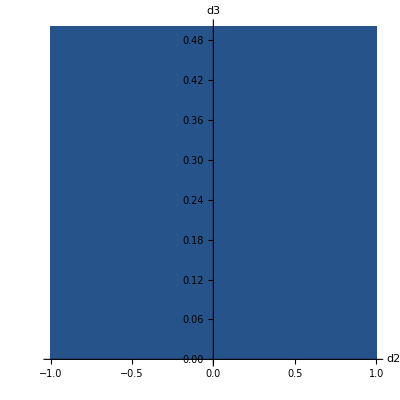

-Graphics-

```mathematica
corrw=remw*uw//Expand[#]&
corrwlist=NoiseMoments[#,{um,ux,uw,uy}]&/@List@@corrw
corrwsum=Total[corrwlist]//Simplify
corrwsimple=corrwsum/.{Subscript[σ, "ux"]->1,Subscript[σ, "uw"]->1,Subscript[σ, "um"]->1,b->1,c->1,d[1]->1,e[1]->1}

corrx=remw*ux//Expand[#]&
corrxlist=NoiseMoments[#,{um,ux,uw,uy}]&/@List@@corrx;
corrxsum=Total[corrxlist]//Simplify
corrxsimple=corrxsum/.{Subscript[σ, "ux"]->1,Subscript[σ, "uw"]->1,Subscript[σ, "um"]->1,b->1,c->1,d[1]->1,e[1]->1}


remcorrwplote[e2_,e3_]:=corrwsimple/.{e[2]->e2,e[3]->e3}
makecorrwplote[]:=ContourPlot[remcorrwplote[e2,e3],{e2,-1,1},{e3,-1,1},ContourLabels->True,Frame->False,Axes->True,AxesLabel->Automatic];
remcorrwplotd[d2_,d3_]:=corrwsimple/.{d[2]->d2,d[3]->d3}
makecorrwplotd[]:=ContourPlot[remcorrwplotd[d2,d3],{d2,-1,1},{d3,0,0.5},ContourLabels->True,Frame->False,Axes->True,AxesLabel->Automatic,Contours->6];
remcorrwplotde[d2_,e2_]:=corrwsimple/.{d[2]->d2,e[2]->e2}
makecorrwplotde[]:=ContourPlot[remcorrwplotde[d2,e2],{d2,0,2},{e2,0,2},ContourLabels->True,Frame->False,Axes->True,AxesLabel->Automatic];
If[orderd>=3,makecorrwplotd[],If[ordere>=3,makecorrwplote[],makecorrwplotde[]]]

remcorrxplote[e2_,e3_]:=corrxsimple/.{e[2]->e2,e[3]->e3}
makecorrxplote[]:=ContourPlot[remcorrxplote[e2,e3],{e2,-1,1},{e3,-1,1},ContourLabels->True,Frame->False,Axes->True,AxesLabel->Automatic];
remcorrxplotd[d2_,d3_]:=corrxsimple/.{d[2]->d2,d[3]->d3}
makecorrxplotd[]:=ContourPlot[remcorrxplotd[d2,d3],{d2,-1,1},{d3,0,0.5},ContourLabels->True,Frame->False,Axes->True,AxesLabel->Automatic,Contours->6];
remcorrxplotde[d2_,e2_]:=corrxsimple/.{d[2]->d2,e[2]->e2}
makecorrxplotde[]:=ContourPlot[remcorrxplotde[d2,e2],{d2,0,2},{e2,0,2},ContourLabels->True,Frame->False,Axes->True,AxesLabel->Automatic];
If[orderd>=3,makecorrxplotd[],If[ordere>=3,makecorrxplote[],makecorrxplotde[]]]
```

{1,2}

3

<||>

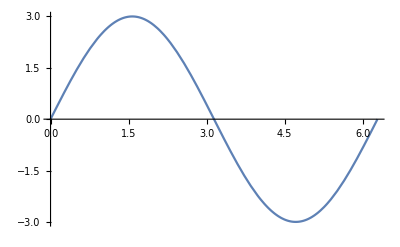
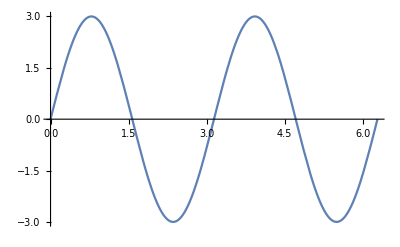
<|myInputValues[3,1]→-Graphics-,myInputValues[3,2]→-Graphics-|>

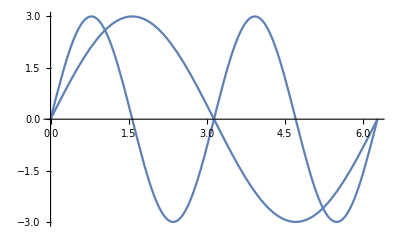

```mathematica
inputValues={1,2}
someParameter=3
crazyCode[input_]:=Plot[someParameter Sin[input x],{x,0,2 Pi}];
resultingPlotList=Association[] (*intialisation of the results*)
AppendTo[resultingPlotList,myInputValues[someParameter,#]->crazyCode[#]]&/@inputValues;
(* :or any kind of iteration you have*)
resultingPlotList
resultingPlotList//Values//Show
```